```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Get["PlotStyles.m"]
```

/Users/yorickreum/PycharmProjects/pytorch_pde/approximator/examples/richards/results-thesis/example-run

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
```

```mathematica
OverleafPath = "/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)"
```

/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)

```mathematica
(* TrainingDir = "richards-2/1"; *)
TrainingDir = "2021-03-19-21-23-53-510723";
```

```mathematica
LossesData = Import[FileNameJoin[{TrainingDir,"losses.csv"}]]
```

{{0.978624990399472483},{0.886086960953559322},{0.802619985944299952},{0.725978646602085664},540867,{0.00310161516646416348},{0.00500310186330923338},{0.00385569707690683241},{0.002742027965787713}}
 |  |  |  |

```mathematica
ListLinePlot[Flatten@LossesData, ScalingFunctions->"Log", PlotTheme->"Detailed", ImageSize->Large]
```

-Graphics-

```mathematica
LossesInterpolation = Interpolation[Flatten@LossesData, InterpolationOrder->5]
```

InterpolatingFunction[{{1.000000000000000000, 511373.000000000000}}, <>]

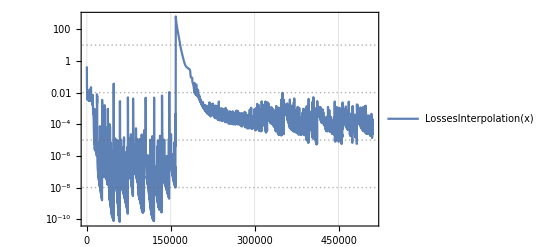

```mathematica
Plot[
LossesInterpolation[x],
Flatten@Join[{x},Rationalize@LossesInterpolation["Domain"]],
ScalingFunctions->"Log",
PlotTheme->"Detailed"
]
```

```mathematica
dataRaw =Import[FileNameJoin[{TrainingDir,"training.csv"}], "Dataset", HeaderLines-> 1]
runRaw = First@dataRaw;
```

```mathematica
duration = DateDifference[FromUnixTime[runRaw["# time start"]/1000], FromUnixTime[runRaw["time end"]/1000]]
UnitConvert[duration, "Hours"]
```

0.254222 days

6.10132 h

```mathematica
runRaw["pretraining best loss epoch"]
```

250990

```mathematica
runRaw["training best loss epoch"]
% + 5 10^4
```

490873

540873